```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/ece1228-electromagnetic-theory" ]
```

/Users/pjoot/project/figures/ece1228-electromagnetic-theory

```mathematica
ClearAll[rot90, bold,fs]
rot90 = {{0,-1},{1,0}}; (*Active rotation by π/2*)

bold = Style[ #, Bold] &;
fs:= Style[ #, FontSize -> 16 ]&;
```

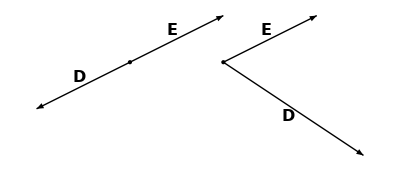

```mathematica
ClearAll[o,e1,e2,d1,d2]
o = {0,0};
o2 = {2,0};
e1 = {2,1};
e2 = e1;
d1 = -e;
d2 = {3,-2};

p = Graphics[
{
Thick,
Arrow[{
{o,e1},{o,d1},{o2,o2+e2}, {o2,o2+d2}
}],
Text["E"// bold//fs, e1/2 + 0.2 rot90.(e2 // Normalize)],
Text["D"// bold//fs, d1/2 + 0.2 rot90.(-d1 // Normalize)],
Text["E"// bold//fs, o2 + e2/2 + 0.2 rot90.(e2 // Normalize)],
Text["D"// bold//fs, o2 + d2/2 + 0.2 rot90.(-d2 // Normalize)],
PointSize -> Large,
Point[o],
Point[o2]
}
]
```

```mathematica
peeters`exportForLatex["constituativeRelationsL2Fig4", p]
```

{constituativeRelationsL2Fig4.eps,constituativeRelationsL2Fig4pn.png}